```mathematica
(* constants*)
(*https://en.wikipedia.org/wiki/Avogadro_constant*)
N0=6.02214076*10^23;
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
me=9.10938291*10^(-28);
mev=0.510998928;
(*single monopole charge*)
Qm=2*Pi*hbar/e;
(*http://en.wikipedia.org/wiki/Fine-structure_constant*)
α=1/137.035999206;
αw=0.42541281596347497;
(*From:https://en.wikipedia.org/wiki/Fermi%27s_interaction*)
Gf=1.4327038609285911*^-49;
Ω=0.0078749969978123844;
kb=1.380658*10^(-16);
omega=0.00787499699;
mH=126*10^3*me/mev;
mp=1.672621777*10^(-24);
mn=1838.6402*me;
(*http://en.wikipedia.org/wiki/Weinberg_angle*)
θw0=0.231208;
θwrad=ArcSin[Sqrt[0.231208]];
θwdeg=θwrad*180/Pi;
(*https://en.wikipedia.org/wiki/Precision_tests_of_QED*)
g=2*1.00115965218085;
(* unification mass:anti-deSitter model*)
muni=3.6543166832631125*^-12;
mtau=1776.82*me/mev;
mmu=105.6583715*me/mev;
mpi=139.57018*me/mev;
mhiggs=126*10^3*me/mev;
mz=91.1876*10^3*me/mev;
mw=80.4335*10^3*me/mev;
mtop=172.76*10^3*me/mev;
mbottom=4.1*10^3*me/mev;
mcharm=1.275*10^3*me/mev;
mstrange=92.4*me/mev;
momegassb=6054.4/10^3;
mplanck=Sqrt[hbar*c/G];
mup=2.01*me/mev;
md0=4.79*me/mev;
(* log linear fit for 4th level quarks*)
mwhite=1.1677931388727855*^-19;
mblack=1.8611487827001873*^-22;
mout=1.5020666505936996*^-20;
Tvac=2.72548;
(*http://en.wikipedia.org/wiki/Observable_universe*)
ru=8.8*10^28/2;
rplanck=2*Pi*hbar/(mplanck*c);
tplanck=rplanck/c;
(*http://en.wikipedia.org/wiki/Big_Bang*)
(*years*days*hours*minutes*seconds*)
tu=13.798*10^9*365.25*24*60*60;
mnu=1.78266270 * 10^(-33 );
mnumu=6.7978246932973695*^-31;
mnutau=1.1431743145263108*^-29;
(*Weak charge on 5d simplex*)
Cw=(3!*2!)*Det[{{α,0,0,0,0,1},{0,α,0,0,0,1},{0,0,α,0,0,1},{0,0,0,α,0,1},{0,0,0,0,α,1},{0,0,0,0,0,1}}]/5!;
rw=Cw^2/(mnu*c^2);
(*http://www.bottomlayer.com/bottom/deutsch/neutrino.html*)
(* Weeks volume*)
vw=0.94270736277692772092;

(* Thurston-Meyerhoff volume*)
vt=0.981368828892232088914;
(*lepton hyperbolic 3 manifold volume*)
vl=(18/24)*vt;
pizero=134.9766*me/mev;
(* Bohr radius: https://en.wikipedia.org/wiki/Bohr_radius*)
ab=5.2917721067*10^(-9);
(*:https://en.wikipedia.org/wiki/Pion:*)
tpip=2.6033*10^(−8 );
tpiz=8.4*10^(−17);
(* product quarks masses in me*)
mup1=12.239779918021176;mdp1=12.256361761325056;
(* elliptic product quarks for Pi mesons*)
mupi=16.25229214603282;mdpi=16.805755043381577;
mqmu=Sqrt[mmu/me];
mqtau=Sqrt[mtau/me];
(* hadron strange and charm product quark masses*)
mqs=mqtau*mup1/mqmu;
mqc=2*mqs;
ttau=2.932*10^(−13);
tmu=2.1969811*10^(−6);
(*.10https://physicstoday.scitation.org/doi/10.1063/PT.3.4424*)
(*.10https://physics.stackexchange.com/questions/134856/units-of-hubble-time-and-hubble-constant*)
Hcbm=67.4/(3.09*10^19);
Hsnova=74.0/(3.09*10^19);
Hlense=73.3/(3.09*10^19);
Have=73.8/(3.09*10^19);
H0=2.2894835758225842*^-18;
th0=1/H0;
(* CMB age*)
tcmb=372000*365.25*24*60*60;
tsnova=1/Hsnova;
msun=1.9891*10^33;
(*first approximation electron g:single loop GED:weak g'*)
g0=2*(1+α/2);
Clear[g1]
g1=g1/.Solve[(g1/Sqrt[g+g1^2])^2==0.231208,g1][[2]];
(* gravity momemt γ*)
γ=e*G/(hbar*c);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(* anomalous magnetic moment of electron:https://en.wikipedia.org/wiki/Anomalous_magnetic_dipole_moment*)
ae=0.0015865218059;
```

```mathematica
(*.......................................*)
```

```mathematica
(* new approach to the Rainich -Misner-Wheeler "already-Unified" field theory*)
(* Pages 419 to end of Introduction to General Relativity, Adler , Bazin and Schiffer 1965*)
```

```mathematica
(*https://en.wikipedia.org/wiki/Geometrodynamics#:
George Rainich had shown decades earlier that one can obtain the electromagnetic field tensor from the electromagnetic contribution to the stress–energy tensor,which in general relativity is directly coupled to spacetime curvature;Wheeler and Misner developed this into the so-called already-unified field theory which partially unifies gravitation and electromagnetism,yielding charge without charge.*)
```

```mathematica
(*SO(4)group sum matrix*)
```

```mathematica
m[1]={{0,1,-1,1},
{-1,0,1,-1},
{1,-1,0,1},
{-1,1,-1,0}};
```

```mathematica
(*Minkowski metric*)
```

```mathematica
guv={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}

```mathematica
v={1,1,1,-1}
```

{1,1,1,-1}

```mathematica
(*electromagnetic field tensor*)
```

```mathematica
Fuv=(e/Sqrt[r])*m[1].guv
```

{{0./(√(1/m)),(1.02168×10^9)/(√(1/m)),-(1.02168×10^9)/(√(1/m)),-(1.02168×10^9)/(√(1/m))},{-(1.02168×10^9)/(√(1/m)),0./(√(1/m)),(1.02168×10^9)/(√(1/m)),(1.02168×10^9)/(√(1/m))},{(1.02168×10^9)/(√(1/m)),-(1.02168×10^9)/(√(1/m)),0./(√(1/m)),-(1.02168×10^9)/(√(1/m))},{-(1.02168×10^9)/(√(1/m)),(1.02168×10^9)/(√(1/m)),-(1.02168×10^9)/(√(1/m)),0./(√(1/m))}}

```mathematica
(*emergy -momentum tensor as Ricci tensor :Already Unified SO(4) theory*)
```

```mathematica
r=2*Pi*hbar/(m*c)
```

(2.21022×10^-37)/m

```mathematica
Ruv=Fuv.Transpose[Fuv]-guv.Fuv.Transpose[Fuv]/4
```

{{0.+1/4 (0.-3.13147×10^18 m)+3.13147×10^18 m,0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m),0.,0.+1/4 (0.-2.08765×10^18 m)+2.08765×10^18 m},{0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m),0.+1/4 (0.-3.13147×10^18 m)+3.13147×10^18 m,0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m),0.},{0.,0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m),0.+1/4 (0.-3.13147×10^18 m)+3.13147×10^18 m,0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m)},{0.+2.08765×10^18 m+1/4 (0.+2.08765×10^18 m),0.,0.+1/4 (0.-2.08765×10^18 m)-2.08765×10^18 m,0.+3.13147×10^18 m+1/4 (0.+3.13147×10^18 m)}}

```mathematica
(* Ricci scalar reduction*)
```

```mathematica
R=v.Ruv.v
```

0.+3/4 (0.-3.13147×10^18 m)+1/2 (0.-2.08765×10^18 m)+4.17529×10^18 m+3/2 (0.+2.08765×10^18 m)+1/4 (0.+3.13147×10^18 m)

```mathematica
Tuv0=(Ruv-R*guv/2)*c^4/(-8*Pi*G)
```

{{-4.81669×10^47 (0.+1/4 (0.-3.13147×10^18 m)+3.13147×10^18 m+1/2 (0.-6.26294×10^18 m+1/2 (0.+3.13147×10^18 m))),-4.81669×10^47 (0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m)),0.,-4.81669×10^47 (0.+1/4 (0.-2.08765×10^18 m)+2.08765×10^18 m)},{-4.81669×10^47 (0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m)),-4.81669×10^47 (0.+1/4 (0.-3.13147×10^18 m)+3.13147×10^18 m+1/2 (0.-6.26294×10^18 m+1/2 (0.+3.13147×10^18 m))),-4.81669×10^47 (0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m)),0.},{0.,-4.81669×10^47 (0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m)),-4.81669×10^47 (0.+1/4 (0.-3.13147×10^18 m)+3.13147×10^18 m+1/2 (0.-6.26294×10^18 m+1/2 (0.+3.13147×10^18 m))),-4.81669×10^47 (0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m))},{-4.81669×10^47 (0.+2.08765×10^18 m+1/4 (0.+2.08765×10^18 m)),0.,-4.81669×10^47 (0.+1/4 (0.-2.08765×10^18 m)-2.08765×10^18 m),-4.81669×10^47 (0.+3.13147×10^18 m+1/4 (0.+3.13147×10^18 m)+1/2 (0.+1/2 (0.-3.13147×10^18 m)+6.26294×10^18 m))}}

```mathematica
Tuv1={{1/4,0,0,0},{0,1/4,0,0},{0,0,1/4,0},{0,0,0,-3/4}}*m*c^2/(4*Pi*r^3/3)
```

{{4.96805×10^129 m^4,0.,0.,0.},{0.,4.96805×10^129 m^4,0.,0.},{0.,0.,4.96805×10^129 m^4,0.},{0.,0.,0.,-1.49041×10^130 m^4}}

```mathematica
T0=v.guv.Tuv0.v
```

0.-4.81669×10^47 (0.+1/4 (0.-2.08765×10^18 m)-2.08765×10^18 m)+4.81669×10^47 (0.+1/4 (0.-2.08765×10^18 m)+2.08765×10^18 m)-1.44501×10^48 (0.-2.08765×10^18 m+1/4 (0.+2.08765×10^18 m))-4.81669×10^47 (0.+2.08765×10^18 m+1/4 (0.+2.08765×10^18 m))+4.81669×10^47 (0.+3.13147×10^18 m+1/4 (0.+3.13147×10^18 m)+1/2 (0.+1/2 (0.-3.13147×10^18 m)+6.26294×10^18 m))-1.44501×10^48 (0.+1/4 (0.-3.13147×10^18 m)+3.13147×10^18 m+1/2 (0.-6.26294×10^18 m+1/2 (0.+3.13147×10^18 m)))

```mathematica
T1=FullSimplify[Det[Tuv1]^(1/4)]
```

6.538318894783239×10^129 (-m^16)^(1/4)

```mathematica
m/.NSolve[T0-T1==0,m]
```

```mathematica
Abs[{6.8841214093875465*^-22+6.8841214093875465*^-22 ⅈ,9.403884727959722*^-22-2.5197633185721754*^-22 ⅈ,9.403884727959722*^-22+2.5197633185721754*^-22 ⅈ,0.,0.,0.,0.}]
```

{9.73562×10^-22,9.73562×10^-22,9.73562×10^-22,0.,0.,0.,0.}

```mathematica
{0.,-((6.002519525562156+1.6083702594264255 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),-((6.002519525562156-1.6083702594264255 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),-((4.394149266135731+4.394149266135731 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),-((4.394149266135731-4.394149266135731 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),-((1.6083702594264255+6.002519525562156 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),-((1.6083702594264255-6.002519525562156 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),((1.6083702594264255-6.002519525562156 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),((1.6083702594264255+6.002519525562156 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),((4.394149266135731-4.394149266135731 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),((4.394149266135731+4.394149266135731 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),((6.002519525562156-1.6083702594264255 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3),((6.002519525562156+1.6083702594264255 ⅈ) e^(2/3) hbar^(2/3))/G^(1/3)}
```

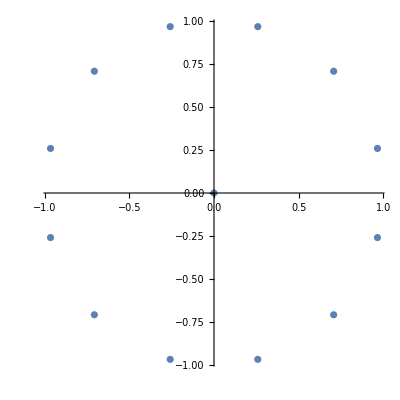

```mathematica
ComplexListPlot[{0.,-9.403884727959746*^-22-2.519763318572182*^-22 ⅈ,-9.403884727959746*^-22+2.519763318572182*^-22 ⅈ,-6.884121409387565*^-22-6.884121409387565*^-22 ⅈ,-6.884121409387565*^-22+6.884121409387565*^-22 ⅈ,-2.519763318572182*^-22-9.403884727959746*^-22 ⅈ,-2.519763318572182*^-22+9.403884727959746*^-22 ⅈ,2.519763318572182*^-22-9.403884727959746*^-22 ⅈ,2.519763318572182*^-22+9.403884727959746*^-22 ⅈ,6.884121409387565*^-22-6.884121409387565*^-22 ⅈ,6.884121409387565*^-22+6.884121409387565*^-22 ⅈ,9.403884727959746*^-22-2.519763318572182*^-22 ⅈ,9.403884727959746*^-22+2.519763318572182*^-22 ⅈ}/9.735617862178854*^-22]
```

```mathematica
9.735617862178854*^-22/mhiggs
```

4.33435

```mathematica
(e^(2/3) hbar^(2/3))/G^(1/3)
```

```mathematica
1.5666562495819689*^-22/mhiggs
```

0.697484

```mathematica
(10 e^(2/3) hbar^(2/3))/(7 G^(1/3))/mhiggs
```

0.996406

```mathematica
w={0.,-9.403884727959746*^-22-2.519763318572182*^-22 ⅈ,-9.403884727959746*^-22+2.519763318572182*^-22 ⅈ,-6.884121409387565*^-22-6.884121409387565*^-22 ⅈ,-6.884121409387565*^-22+6.884121409387565*^-22 ⅈ,-2.519763318572182*^-22-9.403884727959746*^-22 ⅈ,-2.519763318572182*^-22+9.403884727959746*^-22 ⅈ,2.519763318572182*^-22-9.403884727959746*^-22 ⅈ,2.519763318572182*^-22+9.403884727959746*^-22 ⅈ,6.884121409387565*^-22-6.884121409387565*^-22 ⅈ,6.884121409387565*^-22+6.884121409387565*^-22 ⅈ,9.403884727959746*^-22-2.519763318572182*^-22 ⅈ,9.403884727959746*^-22+2.519763318572182*^-22 ⅈ}/9.735617862178854*^-22
```

{0.,-0.965926-0.258819 ⅈ,-0.965926+0.258819 ⅈ,-0.707107-0.707107 ⅈ,-0.707107+0.707107 ⅈ,-0.258819-0.965926 ⅈ,-0.258819+0.965926 ⅈ,0.258819-0.965926 ⅈ,0.258819+0.965926 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.965926-0.258819 ⅈ,0.965926+0.258819 ⅈ}

```mathematica
ExpandAll[Product[x-w[[i]],{i,13}]]//Chop
```

1. x+x^13